```mathematica
SetDirectory[NotebookDirectory[]];
file="../build/0.h5";
```

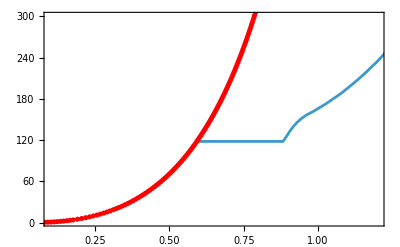
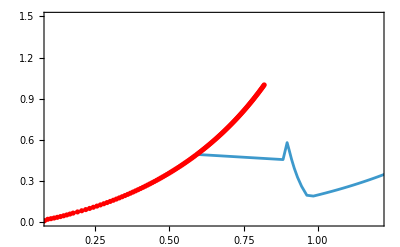
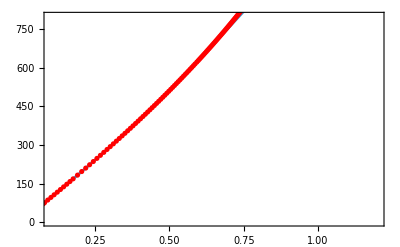

```mathematica
id="1";
n=Import[file,id<>"/EOS/n"];
p=Import[file,id<>"/EOS/p"];
e=Import[file,id<>"/EOS/e"];
cs2=Import[file,id<>"/EOS/cs2"];
ne=Import[file,id<>"/EOSext/n"];
pe=Import[file,id<>"/EOSext/p"];
ee=Import[file,id<>"/EOSext/e"];
cs2e=Import[file,id<>"/EOSext/cs2"];
{Show[ListPlot[Thread[{n,p}],Joined->True],ListPlot[Thread[{ne,pe}],PlotStyle->Red],PlotRange->{{0.1,1.2},{1,300}},Frame->True],Show[ListPlot[Thread[{n,cs2}],Joined->True],ListPlot[Thread[{ne,cs2e}],PlotStyle->Red],PlotRange->{{0.1,1.2},{0,1.5}},Frame->True],Show[ListPlot[Thread[{n,e}],Joined->True],ListPlot[Thread[{ne,ee}],PlotStyle->Red],PlotRange->{{0.1,1.2},{1,800}},Frame->True]}
```